```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"06","18"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\catenoid\horizontal1n

06_18

```mathematica
c=1
X[u_,v_]:={Cosh[v/c] Cos[u],Cosh[v/c] Sin[u],v};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thickness[0.01],Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,0,2Pi},{v,-1.5,1.5},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
```

1

-Graphics3D-

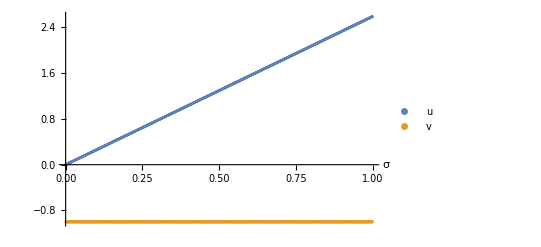

```mathematica
ListPlot[{Reverse[uu],Reverse[vv]},AxesLabel->{σ},PlotLegends->{u,v},DataRange->{0,1}]
ListPlot[vv];
```

```mathematica
Export["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\catenoid\\horizontal1n\\uv.png",%172,"PNG"]
```

D:\Curve Elasticity\Simulation\2026\jan\results\catenoid\horizontal1n\uv.png

```mathematica
4/(Cosh[1])^2 //N
```

1.6799